Reading WARC Records with Mathematica
William J. Turkel and Ian Milligan

Step One: Import the File and Set up a Record

```mathematica
sampleWARCFile="/Users/ianmilligan1/dropbox/git/warcbase-resources/Sample-Data/ARCHIVEIT-227-QUARTERLY-XUGECV-20091218231727-00039-crawling06.us.archive.org-8091.warc.txt";
```

```mathematica
wFile=OpenRead[sampleWARCFile];
```

```mathematica
recordToAssociation[rec_]:=
Module[{recmod,fields,vals},
recmod=StringReplace[rec,"\r\n\r\n"->"\r\n\r\nCONTENT: "];
fields=StringTrim[StringExtract[StringSplit[recmod,"\r"],":"->1]];
vals=Map[StringTrim[StringReplace[#,Shortest[StartOfString~~Except[":"]..]~~":"->""]]&,StringSplit[recmod,"\r"]];
Return[Association[DeleteCases[MapThread[Rule,{fields,vals}],Rule["",""]|Rule["CONTENT",""]]]]]
```

Step Two: Examine the First Records, To Get a Sense of Content

```mathematica
tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0" }];
```

```mathematica
tempRecordAssociation=recordToAssociation[tempRecord];
```

```mathematica
Keys[tempRecordAssociation]
```

{WARC-Type,WARC-Date,WARC-Filename,WARC-Record-ID,Content-Type,Content-Length,CONTENT,ip,hostname,format,conformsTo,operator,publisher,isPartOf,description,robots,http-header-user-agent,http-header-from}

Step Three: Process Content of WARC as Stream, Visualize Metadata Results

Given the list of keys above, sub out in the following. The first step will be to check questions such as hosts. This does so by going through the WARC file, finding all the associations with “Host” and picking them out.

The next command then tallies and prepares them to be visualized, as you see in the PieChart below. This same process can be repeated for others - Content-Type, for example, hostname, operator, publisher, etc. etc. It’s quite flexible. It requires a fair bit of memory and you may see your system overheat.

Interestingly enough, content extraction on many WARCs is quicker.

```mathematica
SetStreamPosition[wFile,1]; (** set the position at 1 **)
```

```mathematica
hosts=Reap[
While[(tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0"}])=!=EndOfFile,tempRecordAssociation=recordToAssociation[tempRecord];
Sow[tempRecordAssociation["Host"]];
]];
```

```mathematica
hostfrequency=Tally[Cases[Flatten[hosts⟦2⟧],Except[_Missing]]]
```

{{v7.lscache3.c.youtube.com,2},{www.davidsuzuki.org,1689},{www.equalvoice.ca,4644},{www.liberal.ca,1968},{www.canadiancrc.com,154},{www.greenparty.ca,15},{greenparty.ca,869},{www.ndp.ca,447},{www.fairvote.ca,465},{www.policyalternatives.ca,596},{podcast.cbc.ca,1},{farm3.static.flickr.com,4},{youtube.com,7},{img.youtube.com,7},{images.ctv.ca,1},{www.partivert.ca,22},{www.gca.ca,2},{www.communitywalk.com,2},{www.flickr.com,1},{vimeo.com,2},{www.oee.nrcan.gc.ca,2},{naturechallenge.org,2},{e-activist.com,2},{www.e-activist.com,2},{www.naturechallenge.org,1},{www.youtube.com,2},{v18.lscache5.c.youtube.com,2},{xfer.ndp.ca,1},{www.cbs.com,1},{v2.cache7.c.youtube.com,1}}

```mathematica
PieChart[hostfrequency[[All,2]],ChartLabels->hostfrequency[[All,1]]]
```

-Graphics-

Step Four : Process Content of WARC as Stream, Explore CONTENT

Content is a bit trickier, because there s quite a bit of mess in there. In general, we may want to do work like visualize a Word Cloud, term frequency, TF-IDF, even working with the strings. We can do all that, luckily.

The following command will look similar.

```mathematica
SetStreamPosition[wFile,1];
content=Reap[
While[(tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0"}])=!=EndOfFile,tempRecordAssociation=recordToAssociation[tempRecord];
Sow[tempRecordAssociation["CONTENT"]];
]];
```

We then need to remove HTML tags, split into words, and then do an assorted bunch of cleaning up. Here it is all together, but as sub commands they are:

Removing HTML tags – note that this might be a good intermediate step to further develop the text analysis side.

```mathematica
notags=StringReplace[Flatten[content⟦2⟧],"<"~~Except[">"]..~~">"->""];
```

Split into words and flatten:

```mathematica
words=Flatten[StringSplit[notags]];
```

Remove all words containing &, /, @, and :

```mathematica
cleaned=Select[words,StringFreeQ[#,{___~~"&"~~___,___~~"/"~~___,___~~"@"~~___,___~~":"~~___,___~~"+"~~___}]&];
```

Remove all one-character words, and put into lowercase:

```mathematica
lowerclean=ToLowerCase[Select[cleaned,StringLength[#]>1&]];
```

But all together is more efficient, as in here:

```mathematica
lowerclean=ToLowerCase[Select[Select[Flatten[StringSplit[StringReplace[Flatten[content⟦2⟧],"<"~~Except[">"]..~~">"->""]]],StringFreeQ[#,{___~~"&"~~___,___~~"/"~~___,___~~"@"~~___,___~~":"~~___,___~~"+"~~___}]&],StringLength[#]>1&]];
```

Then we can create a word cloud, by deleting stopwords.

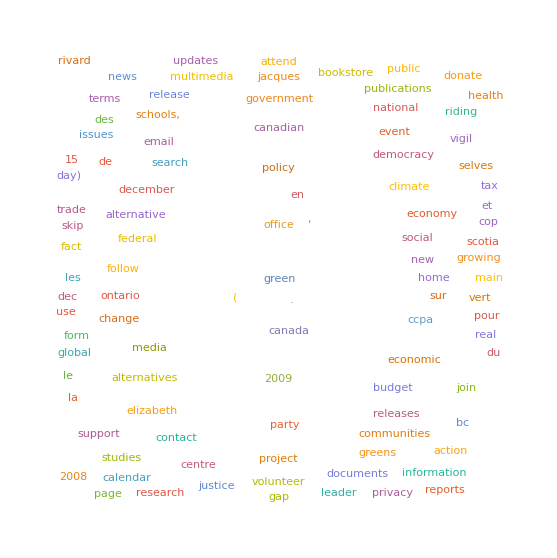

```mathematica
WordCloud[DeleteStopwords[lowerclean]]
```